```mathematica
SetDirectory["~/Code/eeuu/data"]
```

/Users/Alex/Code/eeuu/data

```mathematica
"/Users/Alex/Code/eeuu/data"
Needs["PlotLegends`"]
```

/Users/Alex/Code/eeuu/data

```mathematica
qedDataBelow = Import["qed_below.csv"];
```

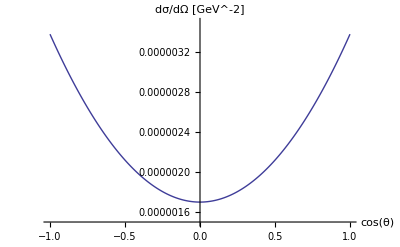

```mathematica
ListLinePlot[qedDataBelow,PlotRange->{1.5*^-6,3.5*^-6},AxesLabel->{Cos[θ],"dσ/dΩ [GeV^-2]"}]
```

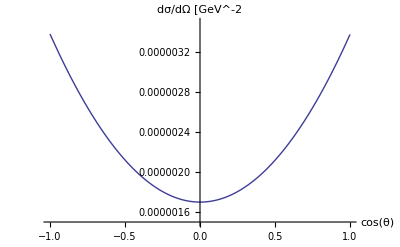

```mathematica
smDataBelow = Import["sm_below.csv"];
ListLinePlot[smDataBelow,PlotRange->{1.5*^-6,3.5*^-6},AxesLabel->{Cos[θ],"dσ/dΩ [GeV^-2]"}]
```

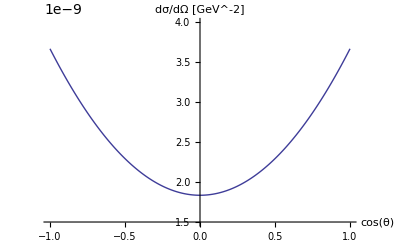

```mathematica
qedDataExact = Import["qed_exact.csv"];
ListLinePlot[qedDataExact,PlotRange->{1.5*^-9,4*^-9},AxesLabel->{Cos[θ],"dσ/dΩ [GeV^-2]"}]
```

```mathematica
smDataExact=Import["sm_exact.csv"];
```

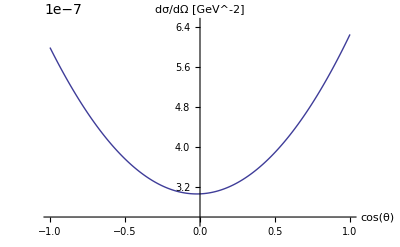

```mathematica
ListLinePlot[smDataExact,PlotRange->{2.5*^-7,6.5*^-7},AxesLabel->{Cos[θ],"dσ/dΩ [GeV^-2]"}]
```

```mathematica
qedDataAbove=Import["qed_above.csv"];
```

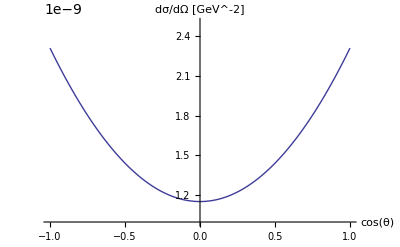

```mathematica
ListLinePlot[qedDataAbove,PlotRange->{1*^-9,2.5*^-9},AxesLabel->{Cos[θ],"dσ/dΩ [GeV^-2]"}]
```

```mathematica
smDataAbove=Import["sm_above.csv"];
```

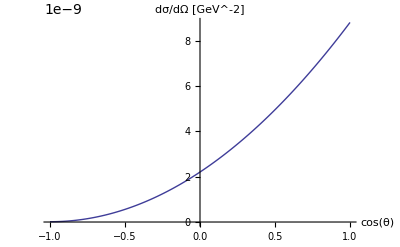

```mathematica
ListLinePlot[smDataAbove,AxesLabel->{Cos[θ],"dσ/dΩ [GeV^-2]"}]
```

```mathematica
mcGammaGammaData=Import["mc_gamma_gamma.csv"];
```

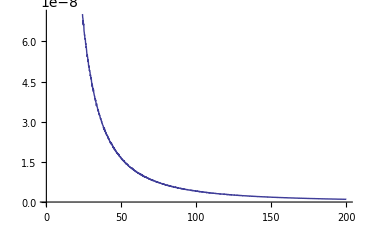

```mathematica
ListLinePlot[mcGammaGammaData]
```

```mathematica
trapGammaGammaData=Import["trap_gamma_gamma.csv"];
```

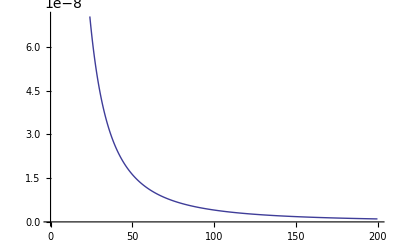

```mathematica
ListLinePlot[trapGammaGammaData]
```

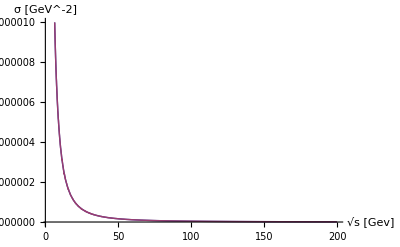

```mathematica
Needs["PlotLegends`"]
ListLinePlot[{trapGammaGammaData,mcGammaGammaData},PlotLegend->{"Trapezium","Monte Carlo"},PlotRange->{0,1*^-6},LegendPosition->{0.4,0.2},LegendShadow->None,LegendBorder->None,LegendTextSpace->6,AxesLabel->{ToString[Sqrt[s],FormatType->StandardForm]<>"\n[Gev]","σ [GeV^-2]"}]
```

```mathematica
trapCombinedData=Import["trap_combined.csv"];
```

```mathematica
mcCombinedData=Import["mc_combined.csv"];
```

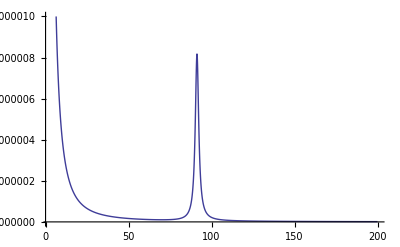

```mathematica
ListLinePlot[trapCombinedData,PlotRange->{0,1*^-6}]
```

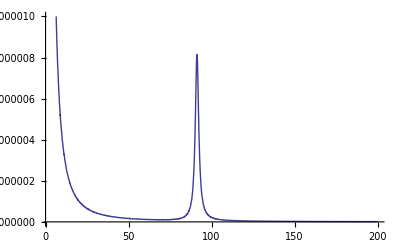

```mathematica
ListLinePlot[mcCombinedData,PlotRange->{0,1*^-6}]
```

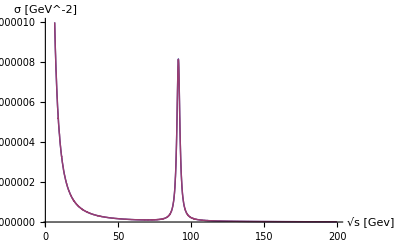

```mathematica
ListLinePlot[{trapCombinedData,mcCombinedData},PlotRange->{0,1*^-6},PlotLegend->{"Trapezium","Monte Carlo"},LegendPosition->{0.4,0.2},LegendShadow->None,LegendBorder->None,LegendTextSpace->6,AxesLabel->{ToString[Sqrt[s],FormatType->StandardForm]<>"\n[Gev]","σ [GeV^-2]"}]
```

```mathematica
trapCombinedFocusedData=Import["trap_combined_focused.csv"];
```

```mathematica
mcCombinedFocusedData=Import["mc_combined_focused.csv"];
```

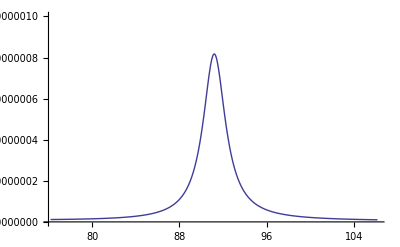

```mathematica
ListLinePlot[trapCombinedFocusedData,PlotRange->{0,1*^-6}]
```

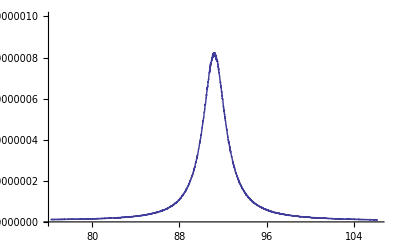

```mathematica
ListLinePlot[mcCombinedFocusedData,PlotRange->{0,1*^-6}]
```

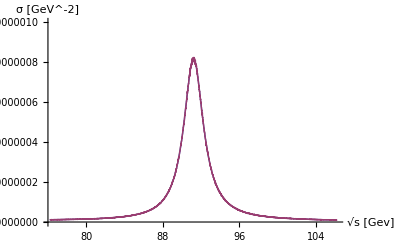

```mathematica
ListLinePlot[{trapCombinedFocusedData,mcCombinedFocusedData},PlotRange->{0,1*^-6},PlotLegend->{"Trapezium","Monte Carlo"},LegendPosition->{0.4,0.2},LegendShadow->None,LegendBorder->None,LegendTextSpace->6,AxesLabel->{ToString[Sqrt[s],FormatType->StandardForm]<>"\n[Gev]","σ [GeV^-2]"}]
```

```mathematica
SetDirectory["~/Code/eeuu/data"]
```

/Users/Alex/Code/eeuu/data

```mathematica
trapGammaZData=Import["trap_gamma_z_focused.csv"];
```

```mathematica
mcGammaZData=Import["mc_gamma_z_focused.csv"];
```

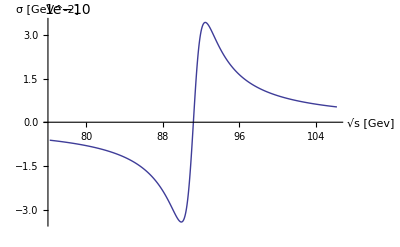

```mathematica
ListLinePlot[trapGammaZData,AxesLabel->{ToString[Sqrt[s],FormatType->StandardForm]<>"\n[Gev]","σ [GeV^-2]"}]
```

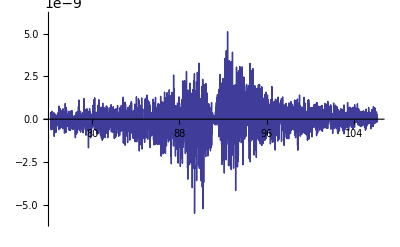

```mathematica
ListLinePlot[mcGammaZData,PlotRange->{-6*^-9,6*^-9}]
```

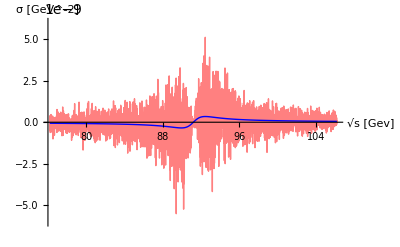

```mathematica
ListLinePlot[{mcGammaZData,trapGammaZData},PlotRange->{-6*^-9,6*^-9},PlotStyle->{RGBColor[1,0.50,0.50],Blue},PlotLegend->{"Monte Carlo","Trapezium"},LegendPosition->{0.4,0.2},LegendShadow->None,LegendBorder->None,LegendTextSpace->6,AxesLabel->{ToString[Sqrt[s],FormatType->StandardForm]<>"\n[Gev]","σ [GeV^-2]"}]
```

```mathematica
diffGammaZData=Import["diffgammaz.csv"];
```

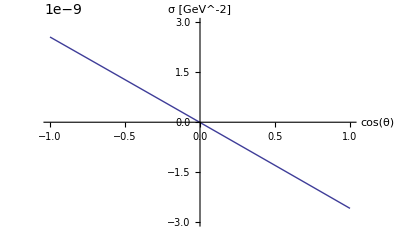

```mathematica
ListLinePlot[diffGammaZData,PlotRange->{-3*^-9,3*^-9},AxesLabel->{Cos[θ],"σ [GeV^-2]"}]
```